This notebook shows cavity optomechanical calculations using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134. See the paper for detailed explanation of the technique. 

If you use this work for research, we would appreciate citing the paper.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

Install the packages MaTeX and CustomTicks to properly generate the figures:

```mathematica
<<MaTeX`
```

```mathematica
Get["CustomTicks`"]
```

************************************************************************************
Below are lists of number of samples P vs CPU times for finding the steady state of the cavity optomechanical oscillator. CPUTabledx is computed using the present method and dx denotes Hilbert space dimension=x. CPUArnoldidx is computed using the sparse Arnoldi iteration. Number of samples go from 10 to 10^5 points. Note that there is a small fluctuations in the CPU times each time one runs the program. See the notebooks {“cavity_optomechanical_cooling_sparse_d10.nb”,”cavity_optomechanical_cooling_sparse_d20.nb”,”cavity_optomechanical_cooling_sparse_d30.nb”, “”cavity_optomechanical_cooling_sparse_d55.nb”} for the actual calculations.

```mathematica
CPUTabled10={{1,0.013547999999999213},{10,0.013897000000000034},{100,0.019206000000000487},{1000,0.05871300000000089},{10000,0.39652000000000065},{100000,3.8654969999999995}};
```

```mathematica
CPUArnoldid10={{1,0.0012340000000037321},{10,0.0069710000000000605},{100,0.0502389999999977},{1000,0.4353569999999962},{10000,4.349566999999993},{100000,43.499748999999994}};
```

```mathematica
CPUTabled20={{1,0.23978500000000033},{10,0.23986499999999997},{100,0.24170600000000061},{1000,0.25530599999999914},{10000,0.35382600000000064},{100000,1.3493139999999997}};
```

```mathematica
CPUArnoldid20={{1,0.006610000000137006},{10,0.11297400000000835},{100,0.9255319999999756},{1000,9.363715000000184},{10000,93.58502500000009},{100000,906.3146270000002}};
```

```mathematica
CPUTabled30={{1,1.5028920000000003},{10,1.5030890000000003},{100,1.5054659999999995},{1000,1.5253729999999976},{10000,1.662810999999999},{100000,3.081557000000001}};
```

```mathematica
CPUArnoldid30={{1,0.040582999999969616},{10,0.36239900000009584},{100,3.1252720000002228},{1000,30.707772999999634},{10000,315.53465300000016},{100000,3029.7268480000007}};
```

```mathematica
CPUTabled55={{1,41.406378000000025},{10,41.40694299999999},{100,41.41221900000003},{1000,41.45147900000001},{10000,41.788095000000006},{100000,45.23162299999999}};
```

```mathematica
CPUArnoldid55={{1,0.19035000000002356},{10,1.6719229999999925},{100,16.847980000000007},{1000,169.62948000000003},{10000,1680.8891400000002},{100000,16834.301218}};
```

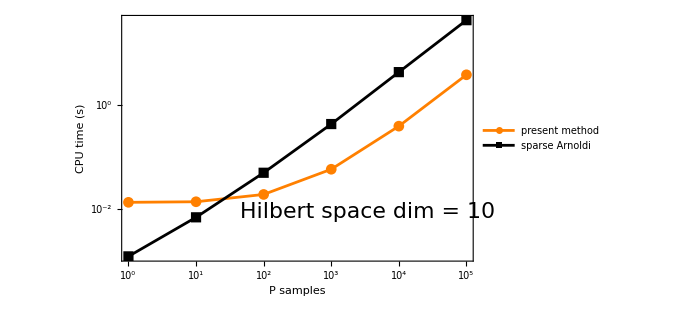

```mathematica
PCPUplotdim10=ListPlot[{Log10[CPUTabled10],Log10[CPUArnoldid10]},FrameLabel->{"P samples","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,FrameTicks->{{LogTicks[-6,2,TickLabelStep->1],None},{LogTicks[0,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},PlotLegends->Placed[LineLegend[{"present method","sparse Arnoldi",""},LegendMarkerSize->{20,10}],{0.3,0.7}],Axes->False,Joined->True,PlotMarkers->Automatic,Epilog->{Text[Style["Hilbert space dim = 10",22,FontFamily->"Times New Roman"],Scaled[{0.7,0.2}]   ]}]
```

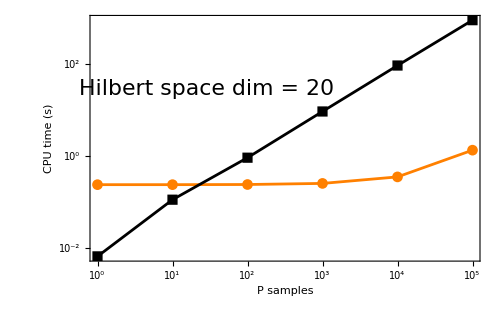

```mathematica
PCPUplotdim20=ListPlot[{Log10[CPUTabled20],Log10[CPUArnoldid20]},FrameLabel->{"P samples","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,FrameTicks->{{LogTicks[-6,3,TickLabelStep->1],None},{LogTicks[0,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0,10}],{0.72,0.18}],Axes->False,Joined->True,PlotMarkers->Automatic,Epilog->{Text[Style["Hilbert space dim = 20",22,FontFamily->"Times New Roman"],Scaled[{0.3,0.7}]   ]}]
```

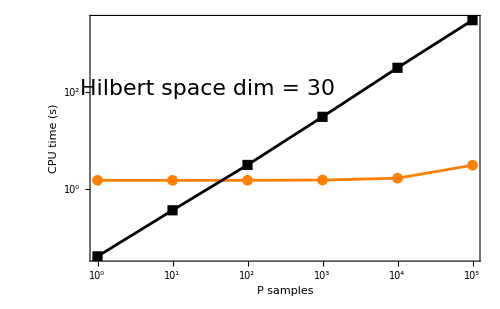

```mathematica
PCPUplotdim30=ListPlot[{Log10[CPUTabled30],Log10[CPUArnoldid30]},FrameLabel->{"P samples","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,FrameTicks->{{LogTicks[-6,4,TickLabelStep->1],None},{LogTicks[0,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0,10}],{0.72,0.18}],Axes->False,Joined->True,PlotMarkers->Automatic,Epilog->{Text[Style["Hilbert space dim = 30",22,FontFamily->"Times New Roman"],Scaled[{0.3,0.7}]   ]}]
```

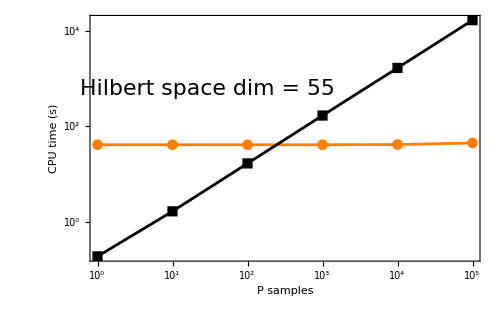

```mathematica
PCPUplotdim55=ListPlot[{Log10[CPUTabled55],Log10[CPUArnoldid55]},FrameLabel->{"P samples","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,FrameTicks->{{LogTicks[-6,4,TickLabelStep->1],None},{LogTicks[0,5,TickLabelStep->1],LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0,10}],{0.72,0.18}],Axes->False,Joined->True,PlotMarkers->Automatic,Epilog->{Text[Style["Hilbert space dim = 55",22,FontFamily->"Times New Roman"],Scaled[{0.3,0.7}]   ]}]
```

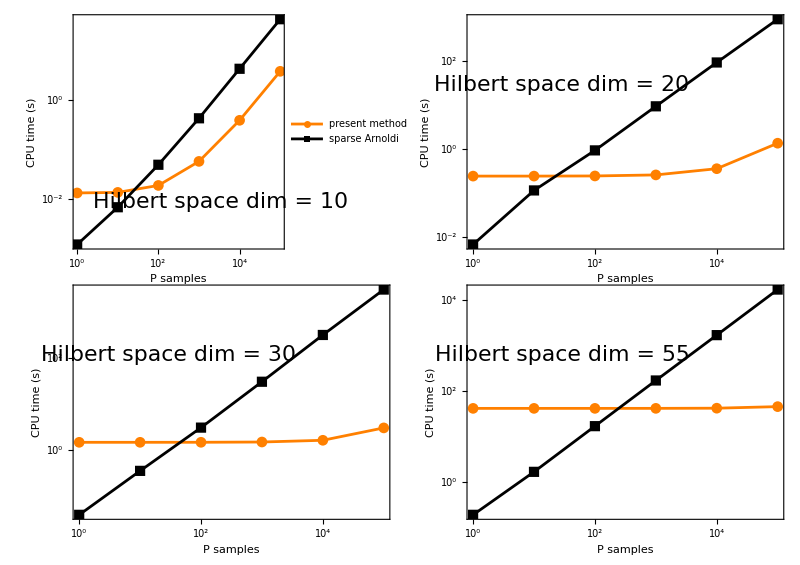

```mathematica
GraphicsGrid[{{PCPUplotdim10,PCPUplotdim20},{PCPUplotdim30,PCPUplotdim55}},ImageSize->Full,Alignment->Center,Spacings->{-15,-30}]
```